```mathematica
getRules[s_,n_]:=ParallelMap[Subscript[#,s,n]&,Range[0,s^(s^n)-1]]
```

```mathematica
evos[rules_,space_]:=Module[{conect,inits},
ParallelTable[
inits=IntegerDigits[#,rules[[i,2]],space]&/@Range[0,rules[[i,2]]^space-1];
conect=Map[
CaArray[rules[[i]],#,1][[1]]->CaArray[rules[[i]],#,1][[2]]&,
inits];
rules[[i]]->Graph[conect],
{i,1,Length[rules]}]
]
```

```mathematica
CaArray[ca_Subscript,s_,t_]:=Module[{},
CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t]
]
```

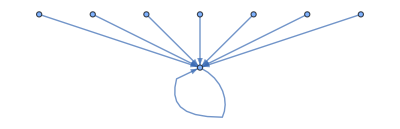
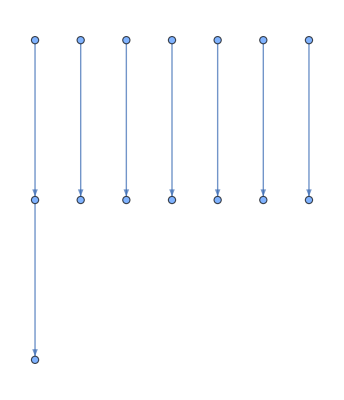
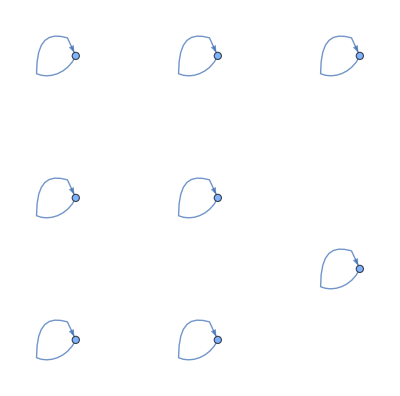
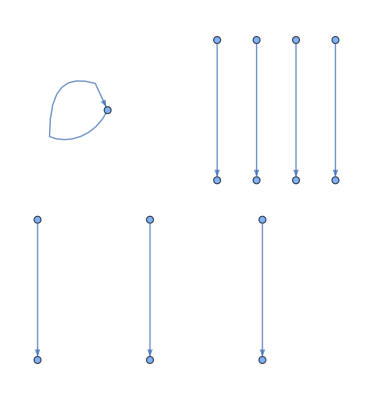
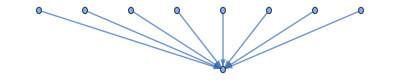
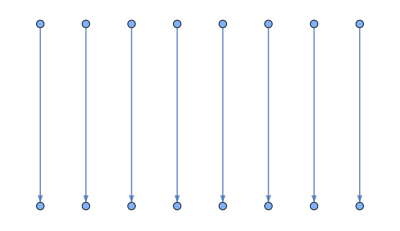
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Total:250 | Total:125 | Total:750 | Total:125 | Total:750 | Total:375 | Total:750
{0_(5,1),6_(5,1),25_(5,1),31_(5,1),50_(5,1),56_(5,1),75_(5,1),81_(5,1),100_(5,1),106_(5,1)} | {1_(5,1),26_(5,1),51_(5,1),76_(5,1),101_(5,1),126_(5,1),151_(5,1),176_(5,1),201_(5,1),226_(5,1)} | {2_(5,1),3_(5,1),4_(5,1),11_(5,1),16_(5,1),21_(5,1),27_(5,1),28_(5,1),29_(5,1),36_(5,1)} | {5_(5,1),30_(5,1),55_(5,1),80_(5,1),105_(5,1),130_(5,1),155_(5,1),180_(5,1),205_(5,1),230_(5,1)} | {7_(5,1),8_(5,1),9_(5,1),10_(5,1),15_(5,1),20_(5,1),32_(5,1),33_(5,1),34_(5,1),35_(5,1)} | {12_(5,1),18_(5,1),24_(5,1),37_(5,1),43_(5,1),49_(5,1),62_(5,1),68_(5,1),74_(5,1),87_(5,1)} | {13_(5,1),14_(5,1),17_(5,1),19_(5,1),22_(5,1),23_(5,1),38_(5,1),39_(5,1),42_(5,1),44_(5,1)}

```mathematica
Gather[evos[getRules[5,1],3],IsomorphicGraphQ[#1[[2]],#2[[2]]]&];
Grid@Transpose[{#[[1,2]],"Total:"<>ToString[Length[#]],#[[;;UpTo[10],1]]}&/@%]
```

```mathematica
evs=Table[
Gather[evos[getRules[5,1],i],IsomorphicGraphQ[#1[[2]],#2[[2]]]&]
,{i,1,6}];
```

```mathematica
Length/@evs
```

{7,7,7,7,7,7}

```mathematica
ListLinePlot[Labeled[#,#,Above]&/@Length/@evs,Filling->Bottom,FillingStyle->Directive[Opacity[0.25],LightBlue],InterpolationOrder->0,PlotRange->All,PlotMarkers->{Automatic,8},PlotStyle->Directive[Thick,RGBColor[0.24,0.55,0.78]],AxesLabel->{"space size","unique behaviours"},ImageSize->400]
```

-Graphics-

```mathematica
wk=Sort/@WeaklyConnectedComponents[Flatten[Values[addData[getRules[2,2]][[{"inverse","mirror"}]]]]];
```

La clasificación que llevabamos a un inicio nos dice que existen 7 comportamientos en 2 estados y 2 vecinos. Ahora, con los grafos de vecindad, vemos que ninguna de las configuraciones iniciales tiene exactamente 7 elementos. Pero el rango de comportamientos oscila entre 9 y 10.

```mathematica
groups=evs[[3,;;,;;,1]]
```

{{0_(2,2),15_(2,2)},{1_(2,2),7_(2,2)},{2_(2,2),11_(2,2)},{3_(2,2)},{4_(2,2),6_(2,2),9_(2,2),13_(2,2)},{5_(2,2)},{8_(2,2),14_(2,2)},{10_(2,2)},{12_(2,2)}}

```mathematica
groups=wk
```

{{2_(2,2),4_(2,2),11_(2,2),13_(2,2)},{1_(2,2),7_(2,2)},{8_(2,2),14_(2,2)},{3_(2,2),5_(2,2)},{10_(2,2),12_(2,2)},{6_(2,2),9_(2,2)},{0_(2,2),15_(2,2)}}

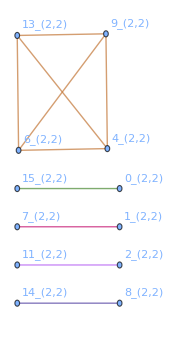

```mathematica
colors=Table[RandomColor[],Length[groups]];

edgesColored=Flatten[Table[Style[#,colors[[i]]]&/@(UndirectedEdge@@@Subsets[groups[[i]],{2}]),{i,Length[groups]}]];

Graph[edgesColored,VertexLabels->"Name"]
```

```mathematica
ic1=Eigenvalues[AdjacencyMatrix[#]]&/@ evos[getRules[2,3][[;;]],4][[;;,2]];
ic2=Eigenvalues[AdjacencyMatrix[#]]&/@ evos[getRules[2,2][[;;]],4][[;;,2]];
```

```mathematica
ic1=Association[#[[1]]->Eigenvalues[AdjacencyMatrix[#[[2]]]]&/@evos[getRules[2,3],4]];
```

```mathematica
ic2=Association[#[[1]]->Eigenvalues[AdjacencyMatrix[#[[2]]]]&/@evos[getRules[2,2],4]];
```

```mathematica
ic1
ic2[[1]]
```

<|0_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},1_(2,3)→{-1,-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0},2_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},3_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0},4_(2,3)→{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},5_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},6_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0,0},7_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},8_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},9_(2,3)→{-1,-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0},10_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0},11_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0},12_(2,3)→{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},13_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},14_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0,0},15_(2,3)→{-1,-1,-1,-1,ⅈ,ⅈ,ⅈ,-ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,1},16_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},17_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0},18_(2,3)→{-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},19_(2,3)→{-1,-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0},20_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0,0},21_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},22_(2,3)→{-1,-1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},23_(2,3)→{-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0,0},24_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},25_(2,3)→{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},26_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},27_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0},28_(2,3)→{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},29_(2,3)→{-1,-1,-1,-1,-1,1,1,1,1,1,1,1,0,0,0,0},30_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0},31_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},32_(2,3)→{-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},33_(2,3)→{-1,-1,-1,-1,1,1,1,1,0,0,0,0,0,0,0,0},34_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0},35_(2,3)→{-1,-1,-1,ⅈ,-ⅈ,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0},36_(2,3)→{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},37_(2,3)→{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},38_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0},39_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0},40_(2,3)→{-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},41_(2,3)→{-1,-1,-1,-1,1,1,1,1,0,0,0,0,0,0,0,0},42_(2,3)→{-1,-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0},43_(2,3)→{-1,-1,-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0},44_(2,3)→{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},45_(2,3)→{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},46_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},47_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0},48_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0},49_(2,3)→{-1,-1,-1,ⅈ,-ⅈ,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0},50_(2,3)→{-1,-1,-1,1,1,1,1,0,0,0,0,0,0,0,0,0},51_(2,3)→{-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1},52_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0},53_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0},54_(2,3)→{-1,-1,-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,0,0,0},55_(2,3)→{-1,-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0},56_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0},57_(2,3)→{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},58_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0},59_(2,3)→{-1,-1,-1,ⅈ,-ⅈ,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0},60_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},61_(2,3)→{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},62_(2,3)→{-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0,0},63_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0},64_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},65_(2,3)→{-1,-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0},66_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},67_(2,3)→{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},68_(2,3)→{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},69_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},70_(2,3)→{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},71_(2,3)→{-1,-1,-1,-1,-1,1,1,1,1,1,1,1,0,0,0,0},72_(2,3)→{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},73_(2,3)→{-1,-1,-1,1,1,1,1,1,1,1,0,0,0,0,0,0},74_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},75_(2,3)→{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},76_(2,3)→{1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0},77_(2,3)→{-1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},78_(2,3)→{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},79_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},80_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0},81_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0},82_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},83_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0},84_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0,0},85_(2,3)→{-1,-1,-1,-1,ⅈ,ⅈ,ⅈ,-ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,1},86_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0},87_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},88_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},89_(2,3)→{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},90_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},91_(2,3)→{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},92_(2,3)→{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},93_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},94_(2,3)→{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},95_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},96_(2,3)→{-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},97_(2,3)→{-1,-1,-1,-1,1,1,1,1,0,0,0,0,0,0,0,0},98_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0},99_(2,3)→{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},100_(2,3)→{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},101_(2,3)→{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},102_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},103_(2,3)→{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},104_(2,3)→{-1,-1,-1,1,1,1,1,1,1,1,1,0,0,0,0,0},105_(2,3)→{-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1},106_(2,3)→{-1,-1,-1,-1,ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0,0},107_(2,3)→{-1,-1,-1,-1,1,1,1,1,0,0,0,0,0,0,0,0},108_(2,3)→{-1,-1,1,1,1,1,1,1,1,1,1,1,1,0,0,0},109_(2,3)→{-1,-1,-1,1,1,1,1,1,1,1,0,0,0,0,0,0},110_(2,3)→{-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},111_(2,3)→{-1,-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0},112_(2,3)→{-1,-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0},113_(2,3)→{-1,-1,-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0},114_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0},115_(2,3)→{-1,-1,-1,ⅈ,-ⅈ,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0},116_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},117_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0},118_(2,3)→{-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0,0},119_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0},120_(2,3)→{-1,-1,-1,-1,ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0,0},121_(2,3)→{-1,-1,-1,-1,1,1,1,1,0,0,0,0,0,0,0,0},122_(2,3)→{-1,-1,-1,1,1,1,1,0,0,0,0,0,0,0,0,0},123_(2,3)→{-1,-1,-1,-1,1,1,1,1,0,0,0,0,0,0,0,0},124_(2,3)→{-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},125_(2,3)→{-1,-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0},126_(2,3)→{-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},127_(2,3)→{-1,-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0},128_(2,3)→{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},129_(2,3)→{-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},130_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0,0},131_(2,3)→{-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0,0},132_(2,3)→{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},133_(2,3)→{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},134_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,1,0,0,0,0},135_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0},136_(2,3)→{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},137_(2,3)→{-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},138_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0},139_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},140_(2,3)→{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},141_(2,3)→{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},142_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0,0,0,0,0},143_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0,0},144_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0,0},145_(2,3)→{-1,ⅈ,-ⅈ,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0,0,0},146_(2,3)→{-1,-1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},147_(2,3)→{-1,-1,-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,0,0,0},148_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,1,0,0,0,0},149_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0},150_(2,3)→{-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1},151_(2,3)→{-1,-1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},152_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0,0},153_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},154_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0},155_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0},156_(2,3)→{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},157_(2,3)→{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},158_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,1,0,0,0,0},159_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0,0},160_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},161_(2,3)→{-1,-1,-1,1,1,1,1,0,0,0,0,0,0,0,0,0},162_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0},163_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0},164_(2,3)→{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},165_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},166_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0},167_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},168_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0},169_(2,3)→{-1,-1,-1,-1,ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0,0},170_(2,3)→{-1,-1,-1,-1,ⅈ,ⅈ,ⅈ,-ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,1},171_(2,3)→{-1,-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0},172_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,1,1,1,0,0,0,0,0,0},173_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},174_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0},175_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0},176_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0},177_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4),0,0,0,0,0},178_(2,3)→{-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0,0},179_(2,3)→{-1,-1,-1,1,1,1,1,0,0,0,0,0,0,0,0,0},180_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0},181_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},182_(2,3)→{-1,-1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},183_(2,3)→{-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},184_(2,3)→{-1,-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0},185_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0},186_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0},187_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0},188_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0,0},189_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},190_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0,0},191_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},192_(2,3)→{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},193_(2,3)→{-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},194_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0,0},195_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},196_(2,3)→{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},197_(2,3)→{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},198_(2,3)→{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},199_(2,3)→{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},200_(2,3)→{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0},201_(2,3)→{-1,-1,1,1,1,1,1,1,1,1,1,1,1,0,0,0},202_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,1,1,1,0,0,0,0,0,0},203_(2,3)→{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},204_(2,3)→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},205_(2,3)→{1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0},206_(2,3)→{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},207_(2,3)→{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},208_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0},209_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},210_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0},211_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0},212_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0,0,0,0,0},213_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0,0},214_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,1,0,0,0,0},215_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0,0},216_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,1,1,1,0,0,0,0,0,0},217_(2,3)→{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},218_(2,3)→{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},219_(2,3)→{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},220_(2,3)→{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},221_(2,3)→{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},222_(2,3)→{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},223_(2,3)→{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},224_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0},225_(2,3)→{-1,-1,-1,-1,ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0,0},226_(2,3)→{-1,-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,0,0,0,0},227_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0},228_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,1,1,1,1,0,0,0,0,0,0},229_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},230_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0,0},231_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},232_(2,3)→{-1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},233_(2,3)→{-1,-1,-1,1,1,1,1,1,1,1,1,0,0,0,0,0},234_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0},235_(2,3)→{-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},236_(2,3)→{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0},237_(2,3)→{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},238_(2,3)→{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},239_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},240_(2,3)→{-1,-1,-1,-1,ⅈ,ⅈ,ⅈ,-ⅈ,-ⅈ,-ⅈ,1,1,1,1,1,1},241_(2,3)→{-1,-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0},242_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0},243_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0},244_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0},245_(2,3)→{-1,-1,ⅈ,ⅈ,-ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0},246_(2,3)→{-1,ⅈ,-ⅈ,1,1,1,0,0,0,0,0,0,0,0,0,0},247_(2,3)→{-1,ⅈ,-ⅈ,1,1,0,0,0,0,0,0,0,0,0,0,0},248_(2,3)→{-1,-1,ⅈ,-ⅈ,1,1,1,1,0,0,0,0,0,0,0,0},249_(2,3)→{-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},250_(2,3)→{-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},251_(2,3)→{-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},252_(2,3)→{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},253_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},254_(2,3)→{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},255_(2,3)→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}|>

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
MatrixPlot[1-DistanceMatrix[Values[ic1],Values[ic2],DistanceFunction->CosineDistance],ColorFunction->"CMYKColors",PlotLegends->Automatic]
```

-Graphics-

```mathematica
reduce=DimensionReduce[ic];
ListPlot[
Labeled[#[[2]],#[[1]]]&/@Transpose[{Range[0,Length[reduce]-1],reduce}],
PlotStyle->PointSize[0.02],PlotRange->All]
```

$Aborted

```mathematica
FindClusters[ic]
```

{{{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0},{1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),0,0,0,0,0,0,0}},{{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0}},{{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{-1,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0}},{{-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1},{-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1},{-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1},{-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1},{-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1},{-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1},{-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1},{-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1},{-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{-1,-1,-1,-1,ⅈ,ⅈ,ⅈ,ⅈ,-ⅈ,-ⅈ,-ⅈ,-ⅈ,1,1,1,1},{-1,-1,-1,-1,ⅈ,ⅈ,ⅈ,ⅈ,-ⅈ,-ⅈ,-ⅈ,-ⅈ,1,1,1,1},{-1,-1,-1,-1,ⅈ,ⅈ,ⅈ,ⅈ,-ⅈ,-ⅈ,-ⅈ,-ⅈ,1,1,1,1},{-1,-1,-1,-1,ⅈ,ⅈ,ⅈ,ⅈ,-ⅈ,-ⅈ,-ⅈ,-ⅈ,1,1,1,1},{-1,-1,-1,-1,ⅈ,ⅈ,ⅈ,ⅈ,-ⅈ,-ⅈ,-ⅈ,-ⅈ,1,1,1,1},{-1,-1,-1,-1,ⅈ,ⅈ,ⅈ,ⅈ,-ⅈ,-ⅈ,-ⅈ,-ⅈ,1,1,1,1}},{{1,1,1,1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{1,1,1,1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{1,1,1,1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{1,1,1,1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{1,1,1,1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{1,1,1,1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{1,1,1,1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{1,1,1,1,1,1,-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)}}}